# Rescaled f(R)Canonical Scalar Field Inflation In The Presence Of A Chern-Simons Term.

## Axionic Inflation With A Power-Law Chern-Simons Scalar Coupling Function.

## 1.Designation Of Scalar Functions, Equations Of Motion, Slow-Roll/Observed Indices.

We start by designating the scalar functions of the model. For simplicity, the Chern-Simons scalar coupling function obtains a power-law form and the scalar potential a trigonometric form. Compatibility is achieved for a quadratic potential but we shall keep it arbitrary for the time being so as to study the dependence of the observed indices, and especially the scalar spectral index ns on such exponent. The equations of motion are extracted by assuming the slow-roll condition is valid. Slow-roll indices along with observed indices are taken from arXiv:0412126.

Every parameter that ends with 1 is an auxiliary free parameter that needs to be designated later. With v and V the Chern-Simons coupling and the scalar potential are denoted while H is Hubble’s parameter and H2 the squared Hubble. Each parameter ending with dot implies time derivative for simplicity and Qt is an auxiliary function that depends on both the scalar field and the polarization of gravitational waves. Finally, indices ε1 through ε3 are the slow-roll indices of the model and ns, nt, r indicate the observed indices.

```mathematica
v[φ_]:=Λ1(κ φ)^p
vdot[φ_]:=D[v[φ],φ]φdot[φ]
V[φ_]:=V1(1+Cos[φ/φ1])
H2[φ_]:=κ^2 V[φ]/(3α)
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=(-D[V[φ],φ])/(3H[φ])
Hdot[φ_]:=-κ^2/(2α)φdot[φ]^2
Qt[λ_,φ_]:=α/κ^2+2λ vdot[φ]H[φ]
ε1[φ_]:=(-Hdot[φ])/H2[φ]
ε2[φ_]:=ε1[φ]-D[V[φ],{φ,2}]/(κ^2 V[φ])
ε6[φ_]:=(D[Qt[1,φ],φ]φdot[φ])/(2H[φ]Qt[1,φ])+(D[Qt[-1,φ],φ]φdot[φ])/(2H[φ]Qt[-1,φ])
ns[φ_]:=1-2(2ε1[φ]+ε2[φ])
nt[φ_]:=-2(ε1[φ]+ε6[φ])
r[φ_]:=8Abs[ε1[φ]](α/Abs[κ^2 Qt[1,φ]]+α/Abs[κ^2 Qt[-1,φ]])
```

## 2. Extracting The Values Of The Scalar Field.

To study the inflationary era, one needs to insert as an input the value of the scalar field during the first horizon crossing to the observed indices. Such a value can be extracted by firstly finding the final value during the ending stage of the inflationary era by imposing that ε1 becomes of order O(1). Afterwards, by using the e-folding number N=∫ Hdt, the initial value can be extracted as a function of N and φf.

I use variable U to denote solutions hereafter while L is a random variable such that the initial value of the scalar field can be extracted.

```mathematica
Clear[κ,Mp,Λ1,V1,N0,φ1,p,α]
U1=Solve[ε1[φ]==1,φ];
φf=φ/.U1[[2]]/.C[1]->0;
L1=Integrate[H[φ]/φdot[φ],φ]/.φ->φl;
L2=Integrate[H[φ]/φdot[φ],φ]/.φ->φk;
U2=Solve[N0==L1-L2,φk];
φi=φk/.U2[[1]]/.{C[1]->0,φl->φf};
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## 3. Designation Of Free Parameters And Validity Of Approximations.

### 3.1. Derivation Of Observed Indices.

By assigning numerical values to the free parameters of the model, the initial value of the scalar field during the first horizon crossing is extracted. Subsequently, one can use such value as an input on the observed indices and derive results. Here, a blue shifted tensor spectral index (nt>0) can be achieved under the slow-roll assumption due to the presence of the Chern-Simons term in the initial gravitational action.

For axions, there is a 95% CL that for N=60, φ1>4 Mp so we are in a good start.  If it can be increased to 10 Mp that’s fine as well (more strict bound). This seems however to produce a blue tilted tensor spectral index, this is fascinating. Note that if φ1 needs to be increased, so does α in order for compatible with the observations results to be produced. (example,φ1=10Mp, α=0.7-0.8)

Tensor spectral index increases with the decrease of Λ1.

```mathematica
κ=1/Mp;Mp=1; Λ1=1;V1=Mp^4;N0=60.;φ1=0.3229Mp;p=4;α=0.0011945; 
φi/Mp//N
φf/Mp//N
φf-φi//N
ns[φ]/.φ->φi//N
nt[φ]/.φ->φi//N
r[φ]/.φ->φi//N
Clear[α,φ1,V1,κ,N0,Mp,Λ1,p]
```

0.507226

0.965636

0.45841

0.966554

-0.0552177

0.000101593

### 3.2. Swampland Criteria.

The first is satisfied in absolute value. One can also exchange the solutions for φi, φf to satisfy it exactly. Changing φi is similar to changing φ\to-φ in the equations so it is like studying natural inflation! In turn, the sign of the second criterion is altered as well. Changing φi and keeping the same values as above changes also the tensor spectral index and becomes red.

-2 φ1 ArcSin[ⅇ^(-(N0 α)/(2 κ^2 φ1^2)) Sin[1/2 ArcTan[(α-2 κ^2 φ1^2)/(α+2 κ^2 φ1^2),(2 √2 √α κ φ1)/(√(α^2+4 α κ^2 φ1^2+4 κ^4 φ1^4))]]]+φ1 ArcTan[(α-2 κ^2 φ1^2)/(α+2 κ^2 φ1^2),(2 √2 √α κ φ1)/(√(α^2+4 α κ^2 φ1^2+4 κ^4 φ1^4))]

-2 φ1 ArcSin[ⅇ^(-(30 α)/φ1^2) Sin[1/2 ArcTan[(α-2 φ1^2)/(α+2 φ1^2),(2 √2 √α φ1)/(√(α^2+4 α φ1^2+4 φ1^4))]]]+φ1 ArcTan[(α-2 φ1^2)/(α+2 φ1^2),(2 √2 √α φ1)/(√(α^2+4 α φ1^2+4 φ1^4))]

General::munfl: Exp[-10500.] is too small to represent as a normalized machine number; precision may be lost.

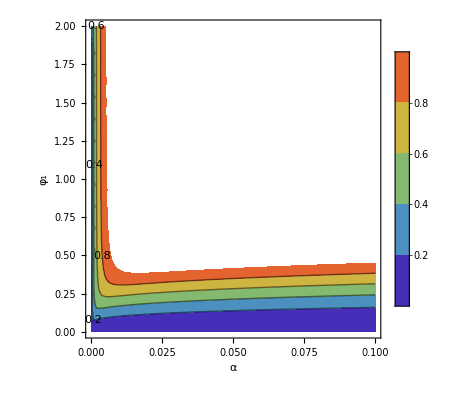

```mathematica
Clear[α,φ1,V2,Λ,m,κ,p,r,φ0,N0] 
Δφ=φf-φi 
κ=1;
N0=60;
Δφ=φf-φi
ContourPlot[Δφ,{α,0,0.1},{φ1,0,2},FrameLabel->{"α","φ_1"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{-1,1}]
(*In my opinion it is a little suprising that there is no dependence on e-folding number*)
(*Successful result. The bounds can be found after a little work but this in not the case here*)
```

The second criterion is also satisfied for small values of α. It can be in agreement with the first.

Abs[Sin[2 ArcSin[ⅇ^(-(N0 α)/(2 κ^2 φ1^2)) Sin[1/2 ArcTan[(α-2 κ^2 φ1^2)/(α+2 κ^2 φ1^2),(2 √2 √α κ φ1)/(√(α^2+4 α κ^2 φ1^2+4 κ^4 φ1^4))]]]]/(φ1 (1+Cos[2 ArcSin[ⅇ^(-(N0 α)/(2 κ^2 φ1^2)) Sin[1/2 ArcTan[(α-2 κ^2 φ1^2)/(α+2 κ^2 φ1^2),(2 √2 √α κ φ1)/(√(α^2+4 α κ^2 φ1^2+4 κ^4 φ1^4))]]]]))]

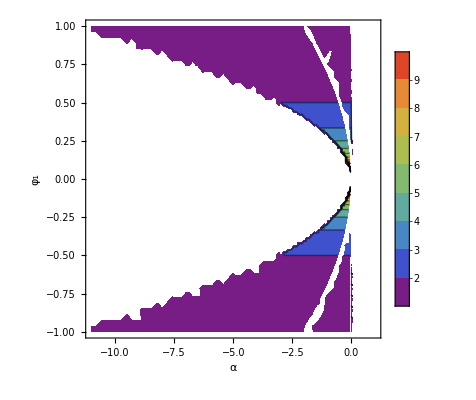

```mathematica
Clear[α,φ1,V2,Λ,m,κ,p,r,φ0,N0] 
Abs[V'[φi]/V[φi]]
κ=1;
N0=60;
Abs[V'[φi]/V[φi]];
ContourPlot[Abs[V'[φi]/V[φi]],{α,-11,1},{φ1,-1,1},FrameLabel->{"α","φ_1"},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
(*Satisfied! Nice result, easy to find the bounds*)
(*The gap around φ0 is strongly connected with the range of the plot. Keep in mind that we need the most general case for the satisafaction of the swampland criteria and since it is imposed theoretically that if one of them is satisfied the concjecture in general is satisfied we can simply gather the different areas that emerge from each different form and then give a more general and also compact result.*)
```

Now the thirds criterion, although it can be satisfied simultaneously with the other two, it requires a small value of the decay constant of axions and thus spoils compatibility with the scalar spectral index. Overall you cannot satisfy everything simultaneously.

Note also that the Swampland criteria are only satisfied if the decay rate is smaller that 3.7 Mp which is the “lowest” bound for the canonical scalar field inflation with 60 efolds, around 95% CL.

Cos[2 ArcSin[ⅇ^(-(N0 α)/(2 κ^2 φ1^2)) Sin[1/2 ArcTan[(α-2 κ^2 φ1^2)/(α+2 κ^2 φ1^2),(2 √2 √α κ φ1)/(√(α^2+4 α κ^2 φ1^2+4 κ^4 φ1^4))]]]]/(φ1^2 (1+Cos[2 ArcSin[ⅇ^(-(N0 α)/(2 κ^2 φ1^2)) Sin[1/2 ArcTan[(α-2 κ^2 φ1^2)/(α+2 κ^2 φ1^2),(2 √2 √α κ φ1)/(√(α^2+4 α κ^2 φ1^2+4 κ^4 φ1^4))]]]]))

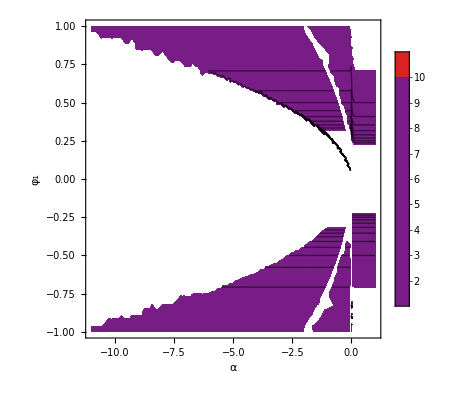

```mathematica
Clear[α,φ1,V2,Λ,m,κ,p,r,φ0,N0] 
-V''[φi]/V[φi]
κ=1;
N0=60;
-V'[φi]/V[φi];
ContourPlot[-V''[φi]/V[φi],{α,-11,1},{φ1,-1,1},FrameLabel->{"α","φ_1"},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{1,10}]
(*In reality we have a similar result with the previous analysis but now we have both in the numerator and denominator  cos and φ0 is squared so this limits*)
```

### 3.3. Ascertaining The Validity Of The Approximations.

The numerical values of the slow-roll indices during the first horizon crossing according to Planck 2018 data must be of order O(10^-3) and lesser. Such results are indicative of the validity of the slow-roll approximations. Slow-roll index ε6 is excluded in this case.

```mathematica
ε1[φ]/.φ->φi//N;
ε2[φ]/.φ->φi//N;
ε6[φ]/.φ->φi//N;
```

Such result is also expected to apply on the self check on the equations of motion.

```mathematica
Hdot[φ]/.φ->φi//N;
H2[φ]/.φ->φi//N;
φdot[φ]^2/2/.φ->φi//N;
V[φ]/.φ->φi//N;
D[φdot[φ],φ]φdot[φ]/.φ->φi//N;
H[φ]φdot[φ]/.φ->φi//N;
```

## 4. Diagrammatic Results.

In this section, it is interesting to examine the area of values for certain auxiliary parameters that result in both a compatible with the observations result and also a blue shifted tensor spectral index.

```mathematica
Clear[α,φ1,V1,κ,N0,Mp,Λ1,p]
Clear[d]
Λ1=1;
V1=1;
κ=1;
N0=60;
nt[φ];
r[φ];
ns[φ];
```

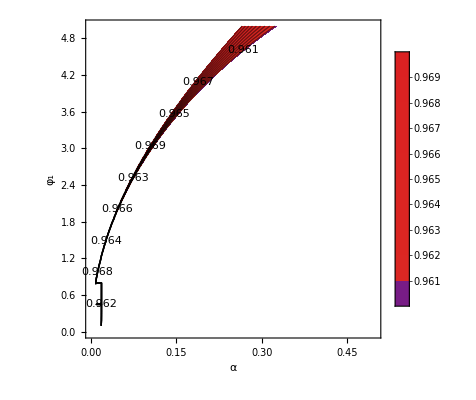

```mathematica
(*Ns*)
ContourPlot[ns[φ]/.φ->φi,{α,0,0.5},{φ1,0.1,5},FrameLabel->{"α","φ_1"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0.9607,0.9691}]
(*For some reason errors occured if the explicit form was used*)
(*Lets zoom in for 3 regions to find info for the monotony*)
```

4 Abs[(α Sin[φ/φ1]^2)/(φ1^2 (1+Cos[φ/φ1])^2)] (α/Abs[α-(4 φ Sin[φ/φ1])/(3 φ1)]+α/Abs[α+(4 φ Sin[φ/φ1])/(3 φ1)])

General::munfl: Exp[-16802.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1076.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4302.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

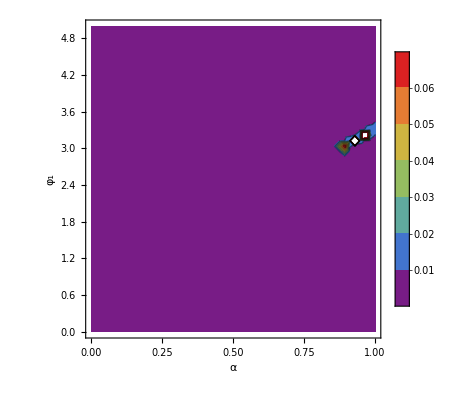

4 Abs[(α Sin[φ/φ1]^2)/(φ1^2 (1+Cos[φ/φ1])^2)] (α/Abs[α-(8 φ^3 Sin[φ/φ1])/(3 φ1)]+α/Abs[α+(8 φ^3 Sin[φ/φ1])/(3 φ1)])

General::munfl: Exp[-16802.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1076.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4302.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

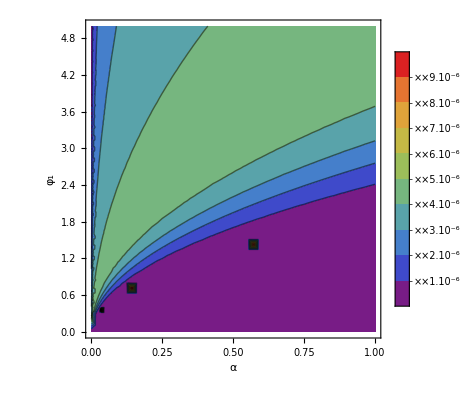

```mathematica
Clear[p]

p=2;
r[φ]
ContourPlot[r[φ]/.φ->φi,{α,0,1},{φ1,0,5},FrameLabel->{"α","φ_1"},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.064}]

Clear[p]
p=4;
r[φ]
ContourPlot[r[φ]/.φ->φi,{α,0,1},{φ1,0,5},FrameLabel->{"α","φ_1"},PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

General::munfl: Exp[-16800.] is too small to represent as a normalized machine number; precision may be lost.

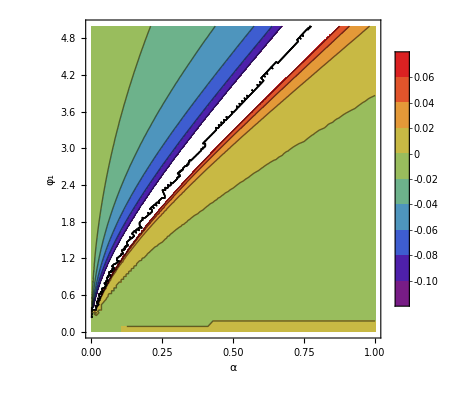

General::munfl: Exp[-16800.] is too small to represent as a normalized machine number; precision may be lost.

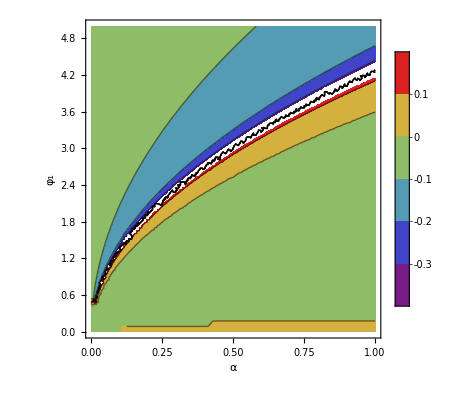

```mathematica
p=2;
ContourPlot[nt[φ]/.φ->φi,{α,0,1},{φ1,0,5},FrameLabel->{"α","φ_1"},PlotLegends->Automatic,ColorFunction->"Rainbow"]

Clear[p]
p=4;
ContourPlot[nt[φ]/.φ->φi,{α,0,1},{φ1,0,5},FrameLabel->{"α","φ_1"},PlotLegends->Automatic,ColorFunction->"Rainbow"]
```